```mathematica
Task 1.
```

```mathematica
h1 = RecurrenceTable[{a[n+1]==2a[n] - n,a[1]==2},a,{n,1, 20}]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
funcp1 = Plot[x+1,{x, 0, 40}, PlotStyle->{Red}];
```

```mathematica
lp1 = ListPlot[h1];
```

```mathematica
funcpl1 = LogPlot[x+1,{x, 0, 40}, PlotStyle->{Red}];
```

```mathematica
llp1 = ListLogPlot[h1];
```

```mathematica
lllp1 = ListLogLogPlot[h1];
```

```mathematica
funcpll1 = LogLogPlot[x+1,{x, 0, 40} , PlotStyle->{Red}];
```

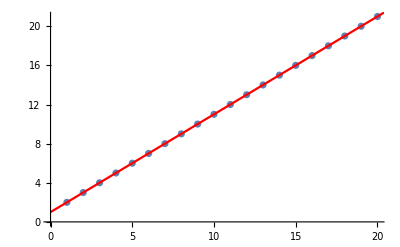

```mathematica
Show[lp1, funcp1, AxesOrigin->{0,0}]
```

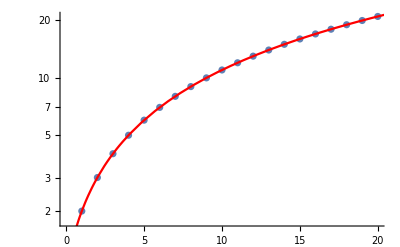

```mathematica
Show[llp1, funcpl1,  AxesOrigin->{0,0}]
```

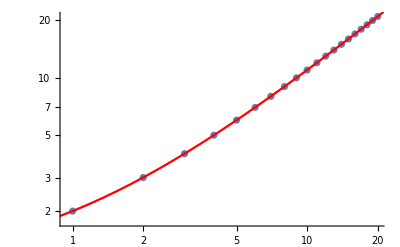

```mathematica
Show[lllp1, funcpll1, AxesOrigin->{0,0}]
```

```mathematica
Task 2.
```

```mathematica
h2 = Table[(1+1/n)^(n+1)-ⅇ, {n, 1, 40}];
```

```mathematica
lp2 = ListPlot[h2];
```

```mathematica
llp2 =ListLogPlot[h2];
```

```mathematica
lllp2 = ListLogLogPlot[h2];
```

```mathematica
funcp21 =Plot[2/x, {x, 0,40}, PlotStyle->{Red}];
funcp22 =Plot[1/x, {x, 0,40}, PlotStyle->{Green}];
```

```mathematica
funcpl21 =LogPlot[2/x, {x, 0,40}, PlotStyle->{Red}];
funcpl22 =LogPlot[1/x, {x, 0,40}, PlotStyle->{Green}];
```

```mathematica
funcpll21 =LogLogPlot[2/x, {x, 0,40}, PlotStyle->{Red}];
funcpll22 =LogLogPlot[1/x, {x, 0,40}, PlotStyle->{Green}];
```

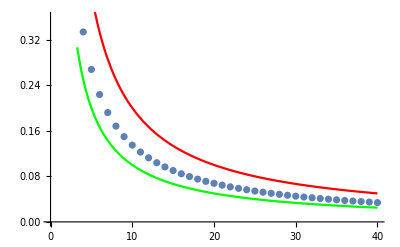

```mathematica
Show[lp2, funcp22, funcp21]
```

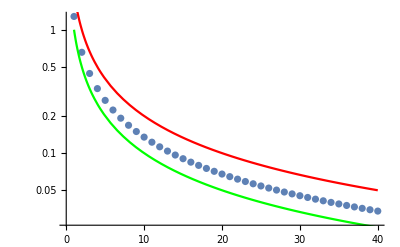

```mathematica
Show[llp2, funcpl22 , funcpl21]
```

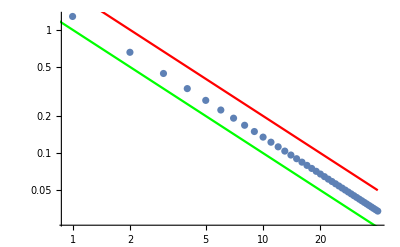

```mathematica
Show[lllp2, funcpll21,funcpll22]
```

```mathematica
Task 3.
```

```mathematica
c[n_, k_]:= (n!)/(k!*(n-k)!)
```

```mathematica
Pask [n_]:= Table[ c[n,k], {k, 0, n}]
```

```mathematica
MatrixForm[Table[Pask[n], {n,0,10}]]
```

({1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1})

```mathematica
PaskRec[n_, k_]:= PaskRec[n-1, k-1] + PaskRec[n-1, k];
PaskRec[n_, 1]:= 1;
PaskRec[n_, n_]:=1
MatrixForm[Table[PaskRec[n,k], {n, 1, 11}, {k, 1, n} ]]
```

({1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1})

```mathematica
Expand[(x+y)^10]
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

```mathematica
Task 4.
```

```mathematica
fa[l_]:= Apply[Plus, l^2]/Length[l]
```

```mathematica
fb[l_]:=Select[l, # <0&] [[1]]
```

```mathematica
fc[l_]:= {Max[l] , Position[l,Max[l]][[1,1]]}
```

```mathematica
Task 5.
```

```mathematica
fib = Table[Fibonacci[n],{n,450}];
```

```mathematica
Length[Select[fib, EvenQ]]
```

150

```mathematica
Length[Select[fib, OddQ]]
```

300

```mathematica
Task 6.
```

```mathematica
f6[x_]:=(ⅇ^(x-1)-1)/(x^2-1);
xo=1;
lim = Limit[f6[x], x->1];
```

```mathematica
xmorexo =  N[Table[Max[ x/.Solve[f6[x]==lim+ 1/10^n, x, Reals]],{n,1,3}]];
xlessxo =  N[Table[Min[ x/.Solve[f6[x]==lim+ 1/10^n, x, Reals]],{n,1,3}]];
delts = Table[Min[Abs[xo - xlessxo[[n]]], Abs[xo - xmorexo[[n]]] ],{n,1,3}];
```

```mathematica
f6plus =  Table[{xmorexo[[n]],f6[xmorexo[[n]]]},{n,1,3}];
```

```mathematica
f6minus = Table[{xlessxo[[n]],f6[xlessxo[[n]]]},{n,1,3}];
```

```mathematica
plusesf6 = Graphics[Point[f6plus]];
minusesf6=Graphics[Point[f6minus]];
deltaGraph= Table[Graphics[{ RGBColor[0,1,0,.1],Rectangle[{xo-delts[[n]],0},{xo+delts[[n]],3}],RGBColor[0,1,0,.5], Line[{{xo-delts[[n]],0},{xo-delts[[n]],3}}], Line[{{xo+delts[[n]],0},{xo+delts[[n]],3}}], Dashed, Black, Line[{{xo,0},{xo,3}}]}], {n, 1, 3}];
```

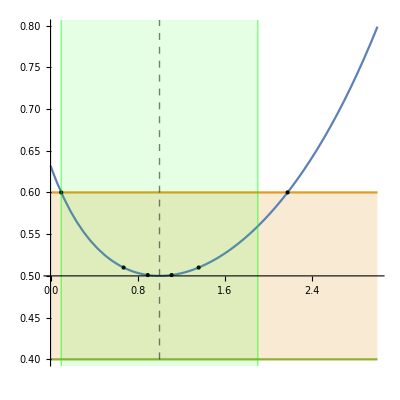

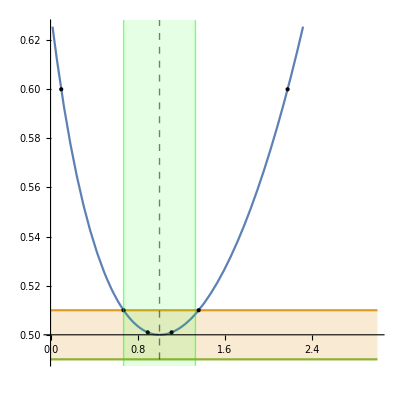

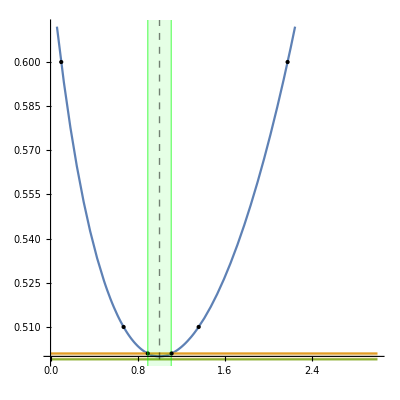

```mathematica
Show[Plot[{f6[x], lim+1/10, lim-1/10},{x, 0, 3}, AxesOrigin->{0,4999999/10000000}, AspectRatio->1, Filling->{2->{3}}], plusesf6, minusesf6, deltaGraph[[1]]]
Show[Plot[{f6[x], lim+1/100, lim-1/100},{x, 0, 3}, AxesOrigin->{0,4999999/10000000}, AspectRatio->1, Filling->{2->{3}}], plusesf6, minusesf6, deltaGraph[[2]]]
Show[Plot[{f6[x], lim+1/1000, lim-1/1000},{x, 0, 3}, AxesOrigin->{0,4999999/10000000}, AspectRatio->1, Filling->{2->{3}}], plusesf6, minusesf6, deltaGraph[[3]]]
```

```mathematica
Task 7.
```

```mathematica
Reduce[ⅇ^(-x^2)-1/5>0,x,Reals]
```

-√Log[5]<x<√Log[5]

```mathematica
Reduce[D[ⅇ^(-x^2)-1/5, x]>0, x, Reals]
```

x<0

```mathematica
Reduce[D[D[ⅇ^(-x^2)-1/5, x],x]>0, x, Reals]
```

x<-1/(√2)||x>1/(√2)

```mathematica
Limit[ⅇ^(-x^2)-1/5, x-> -∞]
```

-1/5

```mathematica
Limit[ⅇ^(-x^2)-1/5, x-> +∞]
```

-1/5

```mathematica
D[ⅇ^(-x^2)-1/5, x]
```

-2 ⅇ^(-x^2) x

```mathematica
-2 ⅇ^(-0.25^2) *0.25
```

-0.469707

```mathematica
kasat[x_]:=ⅇ^(-0.25^2)-1/5 + -2 ⅇ^(-0.25^2) 0.25 * (x-0.25)
```

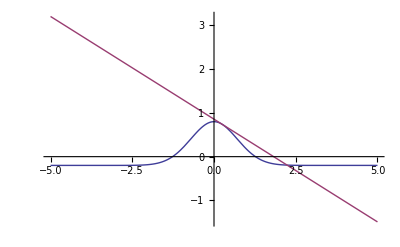

```mathematica
Plot[{ⅇ^(-x^2)-1/5,  kasat[x]},{x, -5, 5}]
```

```mathematica
Task 8.
```

```mathematica
Series[ⅇ^(-x^2)-1/5, {x, 1, 5}]
```

(-1/5+1/ⅇ)-(2 (x-1))/ⅇ+(x-1)^2/ⅇ+(2 (x-1)^3)/(3 ⅇ)-(5 (x-1)^4)/(6 ⅇ)+(x-1)^5/(15 ⅇ)+O[x-1]^6

```mathematica
tey[xo_, n_]:=Normal[Series[ⅇ^(-x^2)-1/5, {x, xo, n}]];
```

```mathematica
teyl[xx_, xo_,n_]:=tey[xo, n]/.x->xx;
```

```mathematica
funcOrig[x_]:=ⅇ^(-x^2)-1/5
```

```mathematica
Lowest=  Table[Abs[teyl[0,1,n] - funcOrig[0]], {n,0, 20}];
Topest = Table[Abs[teyl[2,1,n] - funcOrig[2]], {n,0, 20}];
```

```mathematica
Lowestn = Position[Lowest, Select[Lowest, # ≤ 0.01&] [[1]]][[1,1]]-1 ;
Topestn= Position[Topest, Select[Topest, # ≤ 0.01&] [[1]]][[1,1]] -1;
requiredNumer=Max[Topestn, Lowestn]
```

8

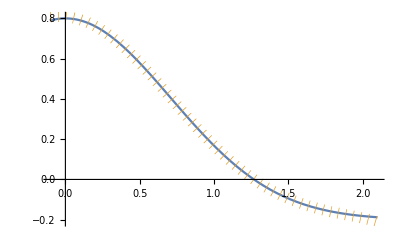

```mathematica
Plot[{funcOrig[y],  teyl[y, 1, requiredNumer]},{y, -0.1, 2.1}, PlotStyle->{{}, {Dotted, Thickness[0.02]}}]
```

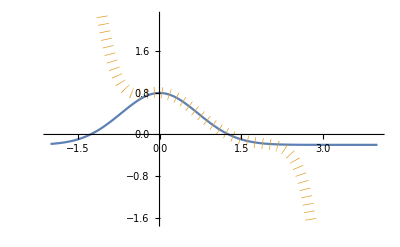

```mathematica
Plot[{funcOrig[y],  teyl[y, 1, requiredNumer]},{y, -2, 4}, PlotStyle->{{}, {Dotted, Thickness[0.02]}}]
```